## Ex

Raketingenjören Pelle avfyrar en raket rakt uppåt från en startramp på marknivå. Raketen
spåras av en radarstation på marknivå som befinner sig på avståndet 3 km från raketens
startramp. Vid en viss tidpunkt efter start registrerar radarstationen att avståndet till raketen
är 5 km och att detta ökar med 5000 km/h. Hur stor är raketens hastighet vid denna tidpunkt?

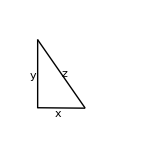

```mathematica
Remove["Global`*"]
```

```mathematica
dydt=Solve[{x[t]^2+y[t]^2==z[t]^2,D[x[t]^2+y[t]^2==z[t]^2,t]},{y[t],y'[t]}]//Last
```

```mathematica
y'[t]/.dydt/.{x[t]->3,x'[t]->0,z[t]->5,z'[t]->5000}
```

alt. skrivsätt

```mathematica
Remove["Global`*"]
```

```mathematica
dydt=Solve[{x^2+y^2==z^2,Dt[x^2+y^2==z^2,t]},{y,Dt[y,t]}]//Last
```

```mathematica
Dt[y,t]/.dydt/.{x->3,Dt[x,t]->0,z->5,Dt[z,t]->5000}
```

## Ex

Bestäm den punkt på kurvan  y=1-x^2 där tangenten till kurvan skär ut den minsta möjliga
triangeln ur första kvadranten.

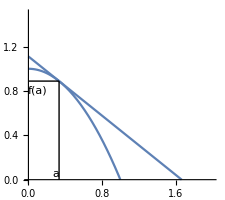

```mathematica
Remove["Global`*"]
```

y-y_0=k(x-x_0)
y=k(x-x_0)+y_0
y=f'(a)(x-a)+f(a)

```mathematica
f[x_]=1-x^2
g[x_]=f'[a](x-a)+f[a]
```

```mathematica
bas=x/.Solve[g[x]==0]//First
höjd=g[0]
```

Triangelarea

```mathematica
Subscript[A, tri]=1/2 höjd*bas
```

```mathematica
Plot[Subscript[A, tri],{a,0,1}]
```

Minsta area

```mathematica
Solve[D[Subscript[A, tri],a]==0.]//Last
```

## Ex

Konstingenjören Sara hänger upp en fin tavla med höjden h på en vägg så att tavlans nedre
kant hamnar sträckan d ovanför Saras ögonhöjd. På vilket avstånd från väggen ska Sara stå
för att hon ska se hela tavlan på bästa sätt? Du kan anta att Sara har mycket bra syn.

-Graphics-

```mathematica
Remove["Global`*"]
```

α=hela vinkeln, β=nedre vinkeln

```mathematica
ekv={Tan[α]==(h+d)/a,Tan[β]==d/a,θ==α-β}
```

```mathematica
Solve[ekv,{θ,α,β}]
```

```mathematica
θ=ArcTan[(h+d)/a]-ArcTan[d/a]
```

derivatan

```mathematica
D[θ,a]
```

Derivatans nollställe

```mathematica
ekv=Solve[D[θ,a]==0,a]//Simplify
```

andra lösningen... det positiva avståndet

```mathematica
a/.ekv⟦2⟧
```

```mathematica
h=1;d=1;
Plot[ArcTan[(h+d)/a]-ArcTan[d/a],{a,0,10},AxesLabel->{a,"θ"}]
```

## Ex

Bestäm de värden på den reella konstanten k för vilka ln(2x)≤k x≤e^(x/2) för alla x>0

```mathematica
Remove["Global`*"]
```

```mathematica
f[x_]:=Log[2x]
g[x_]:=ⅇ^(x/2)
```

```mathematica
Plot[{f[x],g[x]},{x,0,3}]
```

```mathematica
av=Solve[{k==f'[a]==f[a]/a,a>0}]
```

```mathematica
bv=Solve[{k==g'[b]==g[b]/b,b>0}]//First
```

```mathematica
Plot[{f[x],g[x],k x/.av,k x/.bv},{x,0,3},Epilog->{Black,Point[{{ⅇ/2,f[ⅇ/2]},{2,g[2]}}]}]
```

## Ex

Varje sida i en rektangel går genom ett hörn i en mindre rektangel med sidorna a och b. Bestäm
största möjliga arean av den större rektangeln.

```mathematica
Remove["Global`*"]
```

-Graphics-

cos(v)=bas/b, sin(v)=höjd/b, triangelarea=1/2*bas*höjd=1/2*b cos(v)*b sin(v)

```mathematica
tr1=1/2 b^2 Cos[v]Sin[v];
tr2=1/2 a^2 Cos[v]Sin[v];
```

```mathematica
Aavv=Solve[{A==a b+2*1/2 b^2 Cos[v]*Sin[v]+2*1/2 a^2 Cos[v]*Sin[v]}]//Last
```

```mathematica
ekv=Solve[{D[A/.Aavv,v]==0},v](*definitionsmängd?*)
```

maxarea

```mathematica
A/.Aavv/.ekv[[3]]
```

```mathematica
Plot[A/.Aavv/.{a->1,b->2},{v,0,π/2}]
```

## Ex

En 10 m lång stege lutar mot ett 3 m högt staket. Botten av stegen dras bort från staketet
med farten 1.5 m/s. Med vilken fart rör sig toppen av stegen i
i. vertikal riktning
ii. horisontell riktning
då avståndet mellan staketet och stegens botten är 4 m?

-Graphics-

```mathematica
Remove["Global`*"]
```

```mathematica
ekv={(a[t]+x[t])^2+y[t]^2==10^2,y[t]/(a[t]+x[t])==3/x[t]}
```

```mathematica
sys=Join[ekv,D[ekv,t]]
```

```mathematica
lösn=Solve[sys,{y[t],a[t],y'[t],a'[t]}]
```

```mathematica
svar={y[t],y'[t],a[t],a'[t]}/.lösn/.x[t]->4/.x'[t]->3/2//Last
```